```mathematica
Πpar[θ_,v_,mD_]:=mD^2/2((2-2 v^2-v^4 Cos[θ]^2 Sin[θ]^2)/((1-v^2 Sin[θ]^2)^2)-((2+v^2 Sin[θ]^2)(1-v^2)v Cos[θ])/(2(1-v^2 Sin[θ]^2)^(5/2))Log[(v Cos[θ]+√(1-v^2 Sin[θ]^2))/(v Cos[θ]-√(1-v^2 Sin[θ]^2))]);
Πper[θ_,β_,v_,mD_]:=mD^2/2((2-2 v^2-v^4 Cos[β]^2 Sin[θ]^2(1-Cos[β]^2 Sin[θ]^2))/((1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)-((2+v^2-v^2 Cos[β]^2 Sin[θ]^2)(1-v^2)v Cos[β]Sin[θ])/(2(1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)Log[(v Cos[β]Sin[θ]+√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))/(v Cos[β]Sin[θ]-√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))]);
```

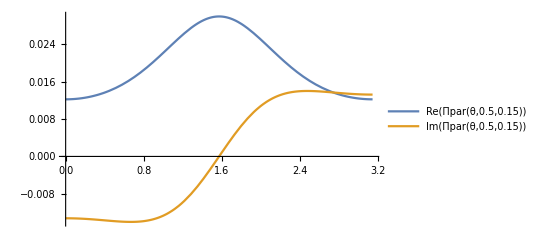

```mathematica
Plot[{Re[Πpar[θ,0.5,0.15]],Im[Πpar[θ,0.5,0.15]]},{θ,0,π},PlotLegends->"Expressions"]
```

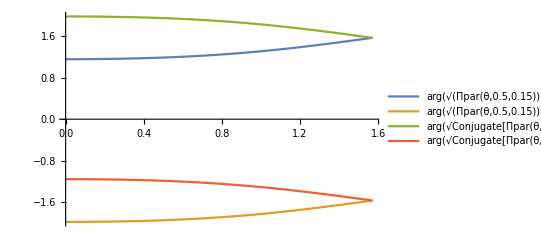

```mathematica
Plot[{Arg[√Πpar[θ,0.5,0.15]]+π/2,Arg[√Πpar[θ,0.5,0.15]]-π/2,Arg[√Conjugate[Πpar[θ,0.5,0.15]]]+π/2,Arg[√Conjugate[Πpar[θ,0.5,0.15]]]-π/2},{θ,0,π/2},PlotLegends->"Expressions"]
```

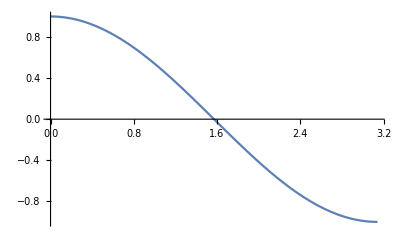

```mathematica
Plot[Cos[x],{x,0,π}]
```

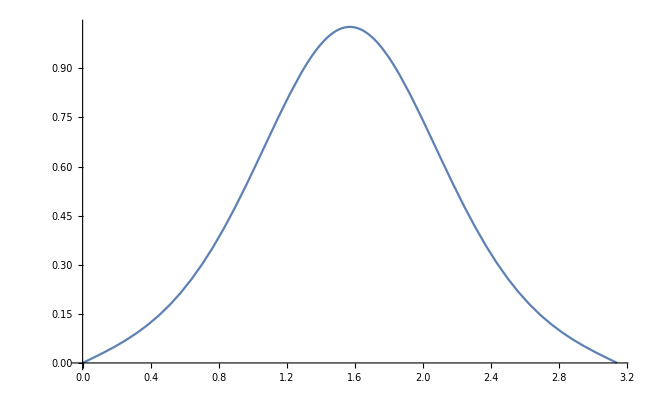

```mathematica
v=0.5;
Plot[(Sin[x](v^2+v^2 Sin[x]^2))/((1-v^2 Sin[x]^2)^(5/2)),{x,0,π}]
```

```mathematica
Integrate[(p Exp[ⅈ p r Cos[θ]])/((p^2+Πpar[θ,v,mD])(p^2+Conjugate[Πpar[θ,v,mD]])),{p,0,∞}]
```

$Aborted

```mathematica
res[θ_,v1_,mD_,r_]:=π/2(Exp[-√Conjugate[Πpar[θ,v1,mD]]r Cos[θ]]/Im[Πpar[θ,v1,mD]]-Exp[-√Πpar[θ,v1,mD]r Cos[θ]]/Im[Πpar[θ,v1,mD]]);
```

```mathematica
res[0.5,0.5,0.15,5]
```

0.+29.1241 ⅈ

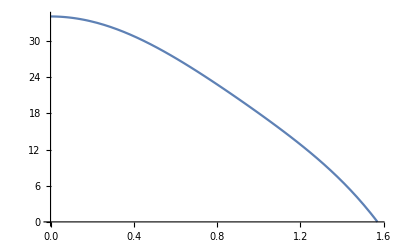

```mathematica
Plot[Im[res[x,0.5,0.15,5]],{x,0,π/2}]
```

```mathematica
NIntegrate[res[x,0.5,0.15,5](Sin[x](2+v^2 Sin[x]^2))/((1-v^2 Sin[x]^2)^(5/2)),{x,0,π/2}]
```

1.46695×10^-15+52.7535 ⅈ

```mathematica
f1[v_,r_,mD_]:=NIntegrate[(Sin[θ](2+v^2 Sin[θ]^2))/((1-v^2 Sin[θ]^2)^(5/2))(p Exp[ⅈ p r Cos[θ]])/((p^2+Πpar[θ,v,mD])(p^2+Conjugate[Πpar[θ,v,mD]])),{θ,0,π},{p,0,∞}]
```

```mathematica
f1[0.5,10,0.15]
```

78.0167+5.64931×10^-10 ⅈ

```mathematica
f1[0.5,20,0.15]
```

32.5067-8.52027×10^-10 ⅈ